-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 5 II. Probability

```mathematica
(*-------------------------------------*)
t1=TimeObject[{7,0,0}];
t2=TimeObject[{7,10,0}];
Lab1="Thermo.&Stat.\nGeneral Picture";
(*-------------------------------------*)
(*-------------------------------------*)
t3=TimeObject[{7,8,0}];
t4=TimeObject[{7,30,0}];
Lab2="Thermo.&Stat.\nMindMap Lecture";
(*-------------------------------------*)
(*-------------------------------------*)
t5=TimeObject[{8,2,0}];
t6=TimeObject[{8,20,0}];
Lab3="Thermo.&Stat.\nStudents talks";
(*-------------------------------------*)
(*-------------------------------------*)
t71=TimeObject[{8,5,0}];
t81=TimeObject[{8,10,0}];
Lab41="Thermo.&Stat.\nBreak";
(*-------------------------------------*)
(*-------------------------------------*)
t7=TimeObject[{7,35,0}];
t8=TimeObject[{8,45,0}];
Lab4="Thermo.&Stat.\nSlides";
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
t72=TimeObject[{8,50,0}];
t82=TimeObject[{9,0,0}];
Lab42=Hyperlink[Style["Thermo.&Stat.\n   Questions?\n   &\n   Chat..."],"https://mmaitex-gemmini.fly.dev/"];

TS1=TimelinePlot[{
Interval[{t1,t2}]->Lab1,
Interval[{t3,t4}]->Lab2,
Interval[{t5,t6}]->Lab3,
Interval[{t71,t81}]->Lab41,
Interval[{t7,t8}]->Lab4,
Interval[{t72,t82}]->Lab42
},
Frame->True,
FrameStyle->Directive[Thickness[0.003],FontFamily->"Comic Sans MS", FontSize->28],
LabelStyle->Directive[FontFamily->"Comic Sans MS",Black,18],ImageSize->800,Background->LightBlue,AspectRatio->0.35
]
```

-Graphics-

## Functions (run cells)

```mathematica
<<MaTeX`
(* ====================================================*)
(* == Para Integrales bonitas == *)
IntegralOperator/:MakeBoxes[IntegralOperator[x__],form_]:=With[{sub=RowBox@BoxForm`MakeInfixForm[{x},",",form]},InterpretationBox[SubscriptBox["∫",sub],IntegralOperator[x]]]
(* ====================================================*)
(* ====================================================*)
(* === Para escribir derivadas muy bonitas ==*)
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
(* == Para derivadas Parciales bonitas == *)
DifferentialOperator/:MakeBoxes[DifferentialOperator[x__],form_]:=With[{sub=RowBox@BoxForm`MakeInfixForm[{x},",",form]},InterpretationBox[SubscriptBox["∂",sub],DifferentialOperator[x]]]
(* ====================================================*)
(* == Para derivadas Totales bonitas == *)
TotalDifferentialOperator/:MakeBoxes[TotalDifferentialOperator[x__],form_]:=With[{sub=RowBox@BoxForm`MakeInfixForm[{x},",",form]},InterpretationBox[SubscriptBox["d",""],TotalDifferentialOperator[x]]]
```

## What we need to know:

### Gaussian distribution 1D:

(ⅇ^(-x^2/2))/(√(2 π))

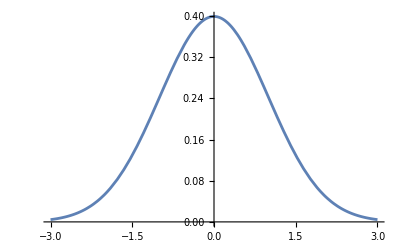

```mathematica
myPDF=PDF[NormalDistribution[0,1],x]
Plot[myPDF,{x,-3,3}]
```

```mathematica
myProba=Integrate[myPDF,{x,0.5,1.0}]
```

0.149882

#### The mean for a gaussian:

```mathematica
myFave=⟨f[x]⟩==Integrate[TraditionalForm[(myPDF)]*f[x],{x,-∞,+∞}];
Framed[MaTeX[myFave,Magnification->5]]
```

-Graphics-

#### In General 1D:

-Graphics-

#### In General 1D:

```mathematica
myFave=⟨f[x]⟩==Integrate[HoldForm[ρ[x]*f[x]],{x,-∞,+∞}];
Framed[MaTeX[myFave,Magnification->5]]
myFave=⟨f[x]⟩==IntegralOperator[x][HoldForm[ρ[x]*f[x]]];
Framed[MaTeX[myFave,Magnification->5]]
```

-Graphics-

-Graphics-

### Differentials

```mathematica
Clear[f,f1,r,x];
Nvars=2;
arg=Sequence[Subscript[x, 1],Subscript[x, 2]];
f1=∑_(i=1)^Nvars TraditionalForm[pdConv[D[f[arg],Subscript[x, i]]]*TotalDifferentialOperator[x][Subscript[x, i]]];
r=TotalDifferentialOperator[x][f[arg]]==f1;
MaTeX[r,Magnification->3]
```

-Graphics-

### Derivatives

```mathematica
Clear[f,x];
f=1/x;
r=DifferentialOperator[x][f]==pdConv[D[f,x]];
MaTeX[r,Magnification->3]
```

-Graphics-

```mathematica
Clear[f,x];
f=Log[x];
r=DifferentialOperator[x][f]==pdConv[D[f,x]];
MaTeX[r,Magnification->3]
```

-Graphics-

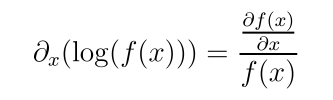

```mathematica
Clear[f,x];
f1=Log[f[x]];
r=DifferentialOperator[x][f1]==pdConv[D[f1,x]];
MaTeX[r,Magnification->3]
```

### Integrals:

```mathematica
Clear[f,x];
f1=1/x;
r=IntegralOperator[x][f1]==Integrate[f1,x];
MaTeX[r,Magnification->3]
```

-Graphics-

### Exponentials

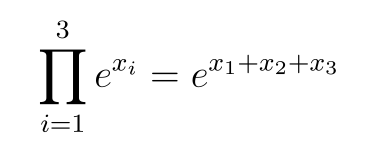

```mathematica
Clear[f,x];
Nvars=3;
f1=∏_(i=1)^Nvars Power[ⅇ,Subscript[x, i]];
r=HoldForm[∏_(i=1)^3 Power[ⅇ,Subscript[x, i]]]==f1;
MaTeX[r,Magnification->4]
```

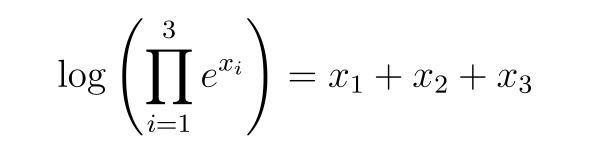

```mathematica
Clear[f,x];
Nvars=3;
f=∏_(i=1)^Nvars Power[ⅇ,Subscript[x, i]];
r=Log[HoldForm[∏_(i=1)^3 Power[ⅇ,Subscript[x, i]]]]==PowerExpand[Log[f]];
MaTeX[r,Magnification->4]
```

### Logarithms

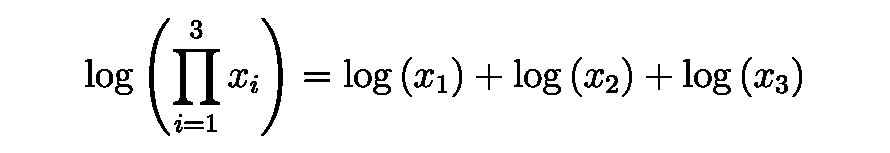

```mathematica
Clear[f];
Nvars=3;
f=∑_(i=1)^Nvars Log[Subscript[x, i]];
r=Log[HoldForm[∏_(i=1)^3 Subscript[x, i]]]==f;
MaTeX[r,Magnification->4]
```

## II.A General Definitions

```mathematica
(1) -- The laws of thermodynamics are derived from observations of macroscopic bodies, capturing their thermal properties. However, matter is composed of atoms and molecules whose motions follow the fundamental laws of classical or quantum mechanics. In principle, it should be possible to deduce the behavior of a macroscopic body from the knowledge of its constituent particles. This is the problem addressed by kinetic theory in the following lectures. Describing the full dynamics of the enormous number of particles involved is a formidable task. As we shall demonstrate, discussing equilibrium properties of a macroscopic system does not require full knowledge of the behavior of its constituent particles. All that is necessary is the likelihood that the particles are in a particular microscopic state. Statistical mechanics is thus an inherently probabilistic description of the system. Familiarity with probability manipulations is therefore an essential prerequisite for statistical mechanics. Our purpose here is to review important results in probability theory and introduce the notations that will be used throughout the course.
```

```mathematica
(2) -- The system under investigation is characterized by a random variable x, which can assume a set of possible values S ≡ {x₁, x₂, ...}. These values can be discrete, as in the case of a coin toss, S_coin = {head, tail}, or a dice throw, S_dice = {1, 2, 3, 4, 5, 6}, or continuous, such as the velocity components of a particle in a gas, S_v = {-∞ < vₓ, vᵧ, vₓ < ∞}, or the energy of an electron in a metal at absolute zero, S_ε = {0 ≤ ε ≤ εᶠ}. An event is defined as any subset of the possible outcomes.
```

```mathematica
(3) -- In the realm of statistical mechanics, we consider a sample space denoted by $\mathcal{S}$, which encompasses all possible outcomes of a given experiment or observation. Within this sample space, we identify a subset $E$, denoted as $E \subset \mathcal{S}$, representing a specific event or collection of outcomes of interest. To quantify the likelihood of this event occurring, we assign a probability $p(E)$. For instance, in the case of rolling a dice, the probability of obtaining the outcome "1" is $p_{\text{dice}}(\{1\})=1/6$, while the probability of obtaining either "1" or "3" is $p_{\text{dice}}(\{1,3\})=1/3$. 

From an axiomatic perspective, the probabilities assigned to events must adhere to the following fundamental conditions:
```

```mathematica
(4) -- In thermodynamics and statistical mechanics, the concept of positivity is a fundamental principle that governs the behavior of probabilities. The statement "p(E) ≥ 0" encapsulates this crucial axiom, which dictates that all probabilities must be non-negative.

This postulate arises from the inherent nature of probabilities, which represent the likelihood of occurrence for specific events or states within a given system. Negative probabilities would violate the very essence of probability theory, as they would imply the possibility of events occurring with negative frequencies, a notion that defies physical reality.

The positivity condition ensures that the probabilities assigned to all possible outcomes or microstates within an ensemble sum up to unity, preserving the conservation of total probability. This property is essential for maintaining the consistency and validity of statistical mechanical calculations, enabling the accurate prediction and analysis of macroscopic thermodynamic quantities derived from the underlying microscopic states.
```

(5) -- The principle of additivity in probability theory states that for two mutually exclusive events, A and B, the probability of their union is equal to the sum of their individual probabilities: p(A or B) = p(A) + p(B). This property holds when the events A and B are disconnected or independent, meaning that the occurrence of one event does not influence the probability of the other event occurring.

(6) -- The normalization condition for a probability distribution function, p(S), states that the sum of probabilities over all possible outcomes in the sample space, S, must equal unity. This requirement arises from the fundamental principle that a random variable must necessarily take on one of the allowed values in its domain. Mathematically, this condition is expressed as:

p(S) = 1

This normalization ensures that the probability distribution function accurately captures the likelihood of all possible events, providing a consistent and coherent framework for statistical analysis and modeling.

```mathematica
(7) -- From a practical point of view, we would like to know how to assign probability values to various outcomes. There are two possible approaches:
```

(8) -- In the realm of Thermodynamics and Mechanical Statistics, the concept of objective probabilities is derived experimentally by observing the relative frequency of an outcome's occurrence across numerous trials of a random variable. Suppose we conduct a random process N times, and during this sequence, a particular event A manifests itself NA times. The objective probability P(A) of event A is then given by the ratio:

P(A) = NA / N

This fundamental relationship encapsulates the essence of objective probabilities, which form the bedrock of statistical mechanics and its applications in understanding the behavior of macroscopic systems from the perspective of their microscopic constituents.

Statistical Mechanics
Ramirez (9)

```mathematica
MaTeX["p(A)=\\lim _{N \\rightarrow \\infty} \\frac{N_{A}}{N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p(A)=\\lim _{N \\rightarrow \\infty} \\frac{N_{A}}{N}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[A]==lim_(N→∞) N_A/N

```mathematica
(10) -- For example, a series of $N=100,200,300$ throws of a dice may result in $N_{1}=$ 19, 30, 48 occurrences of 1 . The ratios .19, .15, . 16 provide an increasingly more reliable estimate of the probability $p_{\text {dice }}(\{1\})$.
```

```mathematica
(11) -- In the realm of Thermodynamics and Statistical Mechanics, subjective probabilities serve as theoretical estimations derived from uncertainties stemming from a lack of precise knowledge regarding potential outcomes. As an illustrative example, consider the assessment p_{dice}({1}) = 1/6, which is grounded in the understanding that a dice throw yields six possible outcomes, and in the absence of any prior evidence suggesting bias, all six outcomes are equally likely to occur. It is crucial to note that all probability assignments in Statistical Mechanics are inherently subjective in nature.

The consequences and implications of such subjective probability assignments must be rigorously validated through empirical measurements and observations. As more information regarding the outcomes becomes available, these subjective probability assignments may require modifications to align with the newly acquired data.
```

## II.B One Random Variable

(12) -- In the realm of Thermodynamics and Mechanical Statistics, we delve into the intricate nature of continuous random variables, as they hold profound relevance to our field of study. Let us consider a random variable x, whose outcomes encompass the entire real number line, symbolically denoted as S_x = {-∞ < x < ∞}. This continuous spectrum of possibilities allows us to capture the inherent complexities and nuances that arise in the analysis of thermodynamic systems and their associated statistical behavior.

The concept of a continuous random variable serves as a powerful tool, enabling us to model and quantify various physical phenomena that exhibit continuous characteristics. By assigning probability distributions to these variables, we can unveil the underlying patterns, trends, and relationships that govern the intricate interplay between energy, entropy, and the microscopic constituents of matter.

Through the lens of continuous random variables, we gain insights into the probabilistic nature of thermodynamic quantities, such as temperature, pressure, and energy levels. These variables act as conduits, bridging the gap between the microscopic realm of individual particles and the macroscopic manifestations observed in bulk systems. By harnessing the mathematical framework of probability theory, we can predict and analyze the collective behavior of countless interacting particles, unveiling the emergent properties that shape the thermodynamic landscape.

### The cumulative probability function (CPF)

(13) -- The cumulative probability function (CPF) P(x) represents the probability that a random variable X takes a value less than or equal to x. It is defined as P(x) = Prob(X ≤ x). This function is a monotonically increasing function of x, ranging from 0 to 1. At negative infinity, the CPF is 0, indicating that there is zero probability of the random variable taking a value less than negative infinity. Conversely, at positive infinity, the CPF is 1, implying that the probability of the random variable being less than or equal to positive infinity is unity.

The CPF is a fundamental concept in probability theory and statistical mechanics, as it provides a comprehensive description of the probability distribution of a random variable. It is particularly useful in calculating probabilities associated with specific intervals or regions of the random variable's domain.

### The probability density function (PDF)

```mathematica
(14) -- The probability density function (PDF), denoted as p(x), represents the derivative of the cumulative distribution function P(x) with respect to x: p(x) = dP(x)/dx. This implies that the probability of an event E occurring within the interval [x, x+dx] is given by p(x)dx. As a probability density, p(x) must be non-negative, and the total probability over the entire domain must be unity, ensuring proper normalization.
```

Statistical Mechanics
Ramirez (16)

```mathematica
MaTeX["\\operatorname{prob.}(\\mathcal{S})=\\int _{-\\infty}^{\\infty}\\, d x p(x)=1", Magnification -> 4]
```

-Graphics-

(17) -- The probability density function, p(x), represents the likelihood of observing a particular value of the random variable x. By its very nature, p(x) is not bounded from above, implying that 0 < p(x) < ∞. This unbounded characteristic is a fundamental property of probability densities, ensuring that no value of x is assigned an infinitely large or infinitesimally small probability.

## MMA exercise (Normal dist.)

```mathematica
myPDF=PDF[NormalDistribution[0,1],x]
Plot[myPDF,{x,-3,3}]
```

(ⅇ^(-x^2/2))/(√(2 π))

-Graphics-

```mathematica
myProba=Integrate[myPDF,{x,-∞,∞}]
```

1

### The expectation value of any function F(x)

```mathematica
(18) -- The expectation value, or the ensemble average, of a function F(x) depending on the random variable $x$, quantifies the mean value that the function would take over numerous realizations of the random process generating x. Mathematically, it is expressed as:

$$\langle F(x) \rangle = \int_{-\infty}^{\infty} F(x) P(x) dx$$

Here, $P(x)$ represents the probability density function associated with the random variable $x$. The expectation value is a crucial concept in statistical mechanics and thermodynamics, as it allows us to calculate the average behavior of macroscopic systems by considering the microscopic states and their respective probabilities.
```

Statistical Mechanics
Ramirez (19)

```mathematica
MaTeX["\\langle F(x)\\rangle=\\int _{-\\infty}^{\\infty}\\, d x p(x) F(x)", Magnification -> 4]
```

-Graphics-

```mathematica
(20) -- The random variable F(x) possesses a probability density function (PDF) p_F(f) df, which represents the probability that F(x) lies within the infinitesimal range [f, f+df]. It is possible for multiple solutions x_i to satisfy the equation F(x) = f, indicating the existence of multiple microstates corresponding to the same macrostate f. This formulation allows for a statistical description of the system, enabling the calculation of various thermodynamic quantities through appropriate ensemble averages.
```

Statistical Mechanics
Ramirez (21)

```mathematica
MaTeX["\\begin{aligned} p_{F}(f) d f=\\sum_{i} p\\left(x_{i}\\right) d x_{i}\\\\ \\Longrightarrow \\quad p_{F}(f)=\\sum_{i} p\\left(x_{i}\\right)\\left|\\frac{d x}{d F}\\right|_{x=x_{i}} \\end{aligned}", Magnification -> 4]
```

-Graphics-

(22) -- In the context of thermodynamics and statistical mechanics, the Jacobian determinant |dx/dF| plays a crucial role when performing a change of variables from x to F in probability density functions (PDFs) or partition functions. This Jacobian factor accounts for the distortion introduced by the transformation, ensuring the proper normalization and conservation of probability.

Consider a one-dimensional PDF p(x) = λ exp(-λ|x|)/2, which represents an exponential distribution. Let us introduce a new variable F(x) = x^2, which maps the original variable x to a quadratic function. To obtain the PDF in terms of F, denoted as p(f), we need to apply the change of variables and include the Jacobian factor |dx/dF|.

The function F(x) = x^2 has two solutions for a given value of f, located at x_± = ± sqrt(f). The corresponding Jacobians are |±f^(-1/2)/2|, accounting for the stretching or compression of the variable space under the transformation. By incorporating these Jacobian factors, we can express the PDF p(f) in terms of the new variable F while preserving the normalization and ensuring the correct probability distribution.

This concept of Jacobian determinants is fundamental in thermodynamics and statistical mechanics when dealing with transformations of variables in partition functions, ensemble averages, or any other statistical quantities involving probability distributions. It guarantees the proper mapping of probabilities between different representations of the system, maintaining the underlying physical principles and ensuring the self-consistency of the theoretical framework.

Statistical Mechanics
Ramirez (23)

```mathematica
MaTeX["\\begin{aligned} P_{F}(f)=\\frac{\\lambda}{2} \\exp (-\\lambda \\sqrt{f})\\left(\\left|\\frac{1}{2 \\sqrt{f}}\\right|+\\left|\\frac{-1}{2 \\sqrt{f}}\\right|\\right)=\\\\ \\frac{\\lambda \\exp (-\\lambda \\sqrt{f})}{2 \\sqrt{f}} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["P_{F}(f)=\\frac{\\lambda}{2} \\exp (-\\lambda \\sqrt{f})\\left(\\left|\\frac{1}{2 \\sqrt{f}}\\right|+\\left|\\frac{-1}{2 \\sqrt{f}}\\right|\\right)=\\frac{\\lambda \\exp (-\\lambda \\sqrt{f})}{2 \\sqrt{f}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

P_F[f]==1/2 λ ⅇ^(-λ √f) (Abs[1/(2 √f)]+Abs[-1/(2 √f)])==(λ ⅇ^(-λ √f))/(2 √f)

(24) -- for $f>0$, and $p_{F}(f)=0$ for $f<0$. Note that $p_{F}(f)$ has an (integrable) divergence at $f=0$.

```mathematica
(25) -- Moments of the probability density function (PDF) represent the expectation values for powers of the random variable. The n^th moment is defined as:

∫(x^n) f(x) dx

where x is the random variable, and f(x) is the probability density function. Moments provide valuable insights into the characteristics of the distribution, such as its central tendency, spread, skewness, and kurtosis. Higher-order moments capture more intricate details about the shape and behavior of the distribution, enabling a comprehensive understanding of the underlying random process.
```

Statistical Mechanics
Ramirez (26)

```mathematica
MaTeX["m_{n} \\equiv\\left\\langle x^{n}\\right\\rangle=\\int  p(x) x^{n}\\,  d x", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["m_{n} \\equiv\\left\\langle x^{n}\\right\\rangle=\\int  p(x) x^{n}\\,  d x",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(m_n≡⟨x^n⟩)==∫p[x] x^nⅆx

(27) -- The characteristic function serves as the generator of moments for a probability distribution. It represents the Fourier transform of the probability density function (PDF), expressed mathematically as:

φ(t) = ∫ exp(itx) f(x) dx

where f(x) is the PDF, and i is the imaginary unit. This compact formulation encapsulates the essential characteristics of the distribution, allowing for the systematic derivation of its moments through differentiation with respect to t, evaluated at t = 0. Consequently, the characteristic function emerges as a powerful tool for exploring the intrinsic properties of random variables and their underlying distributions within the realms of probability theory and statistical mechanics.

## MMA exercise (Normal dist.)

(ⅇ^(-x^2/18))/(3 √(2 π))

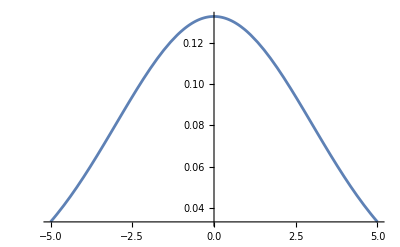

```mathematica
myPDF=PDF[NormalDistribution[0,3],x]
Plot[myPDF,{x,-5,5}]
```

```mathematica
(* mean *)
Echo[Integrate[myPDF*x^1,{x,-∞,∞}], "Mean: "];
(* variance *)
Echo[Integrate[myPDF*x^2,{x,-∞,∞}], "Variance: "];
```

Mean:   0

Variance:   9

Statistical Mechanics
Ramirez (28)

```mathematica
MaTeX["\\tilde{p}(k)=\\left\\langle e^{-i k x}\\right\\rangle=\\int  p(x) e^{-i k x}\\,  d x", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\tilde{p}(k)=\\left\\langle e^{-i k x}\\right\\rangle=\\int  p(x) e^{-i k x}\\,  d x",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p̃[k]==⟨e^(-i k x)⟩==∫p[x] e^(-i k x)ⅆx

(29) -- The characteristic function, denoted by φ(k), encapsulates the complete statistical information of a probability distribution. It is defined as the Fourier transform of the probability density function (PDF), f(x):

φ(k) = ∫ f(x) e^(ikx) dx

Remarkably, this relationship is invertible, allowing us to retrieve the PDF from the characteristic function through the inverse Fourier transform:

f(x) = (1/2π) ∫ φ(k) e^(-ikx) dk

This inverse transformation unveils the underlying probability distribution, enabling us to explore its intrinsic properties and behaviors within the realm of statistical mechanics and thermodynamics.

Statistical Mechanics
Ramirez (30)

```mathematica
MaTeX["p(x)=\\frac{1}{2 \\pi} \\int  \\tilde{p}(k) e^{+i k x}\\,  d k", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p(x)=\\frac{1}{2 \\pi} \\int  \\tilde{p}(k) e^{+i k x}\\,  d k",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[x]==(∫p̃[k] e^(+i k x)ⅆk)/(2 π)

(31) -- Moments of the distribution are obtained by expanding $\tilde{p}(k)$ in powers of $k$,

Statistical Mechanics
Ramirez (32)

```mathematica
MaTeX["\\tilde{p}(k)=\\left\\langle\\sum_{n=0}^{\\infty} \\frac{(-i k)^{n}}{n!} x^{n}\\right\\rangle=\\sum_{n=0}^{\\infty} \\frac{(-i k)^{n}}{n!}\\left\\langle x^{n}\\right\\rangle", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\tilde{p}(k)=\\left\\langle\\sum_{n=0}^{\\infty} \\frac{(-i k)^{n}}{n!} x^{n}\\right\\rangle=\\sum_{n=0}^{\\infty} \\frac{(-i k)^{n}}{n!}\\left\\langle x^{n}\\right\\rangle",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p̃[k]==⟨∑_(n=0)^∞ ((-i k)^n x^n)/(n!)⟩==∑_(n=0)^∞ ((-i k)^n ⟨x^n⟩)/(n!)

```mathematica
(33) -- Moments of the PDF around any point $x_{0}$ can also be generated by expanding
```

Statistical Mechanics
Ramirez (34)

```mathematica
MaTeX["\\begin{aligned} e^{i k x_{0}} \\tilde{p}(k)=\\\\ \\left\\langle e^{-i k\\left(x-x_{0}\\right)}\\right\\rangle=\\sum_{n=0}^{\\infty} \\frac{(-i k)^{n}}{n!}\\left\\langle\\left(x-x_{0}\\right)^{n}\\right\\rangle \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["e^{i k x_{0}} \\tilde{p}(k)=\\left\\langle e^{-i k\\left(x-x_{0}\\right)}\\right\\rangle=\\sum_{n=0}^{\\infty} \\frac{(-i k)^{n}}{n!}\\left\\langle\\left(x-x_{0}\\right)^{n}\\right\\rangle",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

e^(i k x_0) p̃[k]==⟨e^(-i k[x-x_0])⟩==∑_(n=0)^∞ ((-i k)^n ⟨(x-x_0)^n⟩)/(n!)

(35) -- The cumulant generating function is the logarithm of the characteristic function. Its expansion generates the cumulants of the distribution defined through

Statistical Mechanics
Ramirez (36)

```mathematica
MaTeX["\\ln \\tilde{p}(k)=\\sum_{n=1}^{\\infty} \\frac{(-i k)^{n}}{n!}\\left\\langle x^{n}\\right\\rangle_{c}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\ln \\tilde{p}(k)=\\sum_{n=1}^{\\infty} \\frac{(-i k)^{n}}{n!}\\left\\langle x^{n}\\right\\rangle_{c}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ln p̃[k]==∑_(n=1)^∞ ((-i k)^n ⟨x^n⟩_c)/(n!)

(37) -- Relations between moments and cumulants can be obtained by expanding the logarithm of $\tilde{p}(k)$ in eq.(II.7), and using

Statistical Mechanics
Ramirez (38)

```mathematica
MaTeX["\\ln (1+\\epsilon)=\\sum_{n=1}^{\\infty}(-1)^{n+1} \\frac{\\epsilon^{n}}{n}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\ln (1+\\epsilon)=\\sum_{n=1}^{\\infty}(-1)^{n+1} \\frac{\\epsilon^{n}}{n}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Log[1+ϵ]==∑_(n=1)^∞ ((-1)^(n+1) ϵ^n)/n

(39) -- The first four cumulants are called the mean, variance, skewness, and curtosis of the distribution respectively, and are obtained from the moments as

Statistical Mechanics
Ramirez (40)

```mathematica
MaTeX["\\begin{aligned}\\langle x\\rangle_{c} & =\\langle x\\rangle \\\\\\left\\langle x^{2}\\right\\rangle_{c} & =\\left\\langle x^{2}\\right\\rangle-\\langle x\\rangle^{2} \\\\\\left\\langle x^{3}\\right\\rangle_{c} & =\\left\\langle x^{3}\\right\\rangle-3\\left\\langle x^{2}\\right\\rangle\\langle x\\rangle+2\\langle x\\rangle^{3} \\\\\\left\\langle x^{4}\\right\\rangle_{c} & =\\left\\langle x^{4}\\right\\rangle-4\\left\\langle x^{3}\\right\\rangle\\langle x\\rangle-3\\left\\langle x^{2}\\right\\rangle^{2}+12\\left\\langle x^{2}\\right\\rangle\\langle x\\rangle^{2}-6\\langle x\\rangle^{4}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(41) -- The cumulants provide a useful and compact way of describing a PDF.
```

```mathematica
(42) -- An important theorem allows easy computation of moments in terms of the cumulants: Represent the $n^{\text {th }}$ cumulant graphically as a connected cluster of $n$ points. The $m^{\text {th }}$ moment is then obtained by summing all possible subdivisions of $m$ points into groupings of smaller (connected or disconnected) clusters. The contribution of each subdivision to the sum is the product of the connected cumulants that it represents. Using this result the first four moments are easily computed as
```

Statistical Mechanics
Ramirez (43)

```mathematica
MaTeX["\\begin{aligned}\\langle x\\rangle & =\\langle x\\rangle_{c} \\\\\\left\\langle x^{2}\\right\\rangle & =\\left\\langle x^{2}\\right\\rangle_{c}+\\langle x\\rangle_{c}^{2} \\\\\\left\\langle x^{3}\\right\\rangle & =\\left\\langle x^{3}\\right\\rangle_{c}+3\\left\\langle x^{2}\\right\\rangle_{c}\\langle x\\rangle_{c}+\\langle x\\rangle_{c}^{3} \\\\\\left\\langle x^{4}\\right\\rangle & =\\left\\langle x^{4}\\right\\rangle_{c}+4\\left\\langle x^{3}\\right\\rangle_{c}\\langle x\\rangle_{c}+3\\left\\langle x^{2}\\right\\rangle_{c}^{2}+6\\left\\langle x^{2}\\right\\rangle_{c}\\langle x\\rangle_{c}^{2}+\\langle x\\rangle_{c}^{4}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(44) -- This theorem, which is the starting point for various diagrammatic computations is statistical mechanics and field theory, is easily proved by equating the expression in eqs. (II.7) and (II.9) for $\tilde{p}(k)$
```

Statistical Mechanics
Ramirez (45)

```mathematica
MaTeX["\\begin{aligned} \\sum_{m=0}^{\\infty} \\frac{(-i k)^{m}}{m!}\\left\\langle x^{m}\\right\\rangle=\\exp \\left[\\sum_{n=1}^{\\infty} \\frac{(-i k)^{n}}{n!}\\left\\langle x^{n}\\right\\rangle_{c}\\right]= \\\\ \\prod_{n} \\sum_{p_{n}}\\left[\\frac{(-i k)^{n p_{n}}}{p_{n}!}\\left(\\frac{\\left\\langle x^{n}\\right\\rangle_{c}}{n!}\\right)^{p_{n}}\\right] \\end{aligned}", Magnification -> 4]
```

-Graphics-

(46) -- Equating the powers of $(-i k)^{m}$ on the two sides of the above expression leads to

Statistical Mechanics
Ramirez (47)

```mathematica
MaTeX["\\left\\langle x^{m}\\right\\rangle=\\sum_{\\left\\{p_{n}\\right\\}}^{\\prime} \\prod_{n} \\frac{m!}{p_{n}!(n!)^{p_{n}}}\\left\\langle x^{n}\\right\\rangle_{c}^{p_{n}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left\\langle x^{m}\\right\\rangle=\\sum_{\\left\\{p_{n}\\right\\}}^{\\prime} \\prod_{n} \\frac{m!}{p_{n}!(n!)^{p_{n}}}\\left\\langle x^{n}\\right\\rangle_{c}^{p_{n}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨x^m⟩==(∑')_{p_n}∏_n (m! ⟨x^n⟩_c^p_n)/(p_n! (n!)^p_n)

```mathematica
(48) -- In the realm of statistical mechanics, the summation constraint ∑n p_n = m arises from a fundamental principle. This constraint imposes a graphical interpretation where the numerical factor represents the number of ways to distribute m points into clusters of size {p_n}. This encoding captures the essence of particle distributions, laying the foundation for analyzing thermodynamic systems through a statistical lens.
```

## II.C Some Important Probability Distributions

(49) -- In this section, we delve into the properties of three pivotal probability distributions that frequently arise in the realm of thermodynamics and mechanical statistics.

(50) -- (1) The normal (Gaussian) distribution describes a continuous real random variable $x$, with

Statistical Mechanics
Ramirez (51)

```mathematica
MaTeX["p(x)=\\frac{1}{\\sqrt{2 \\pi \\sigma^{2}}} \\exp \\left[-\\frac{(x-\\lambda)^{2}}{2 \\sigma^{2}}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p(x)=\\frac{1}{\\sqrt{2 \\pi \\sigma^{2}}} \\exp \\left[-\\frac{(x-\\lambda)^{2}}{2 \\sigma^{2}}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[x]==exp[-(x-λ)^2/(2 σ^2)]/(√(2 πσ^2))

(52) -- The corresponding characteristic function also has a Gaussian form,(52) -- The Gaussian form of the characteristic function arises from the central limit theorem, which states that the sum of a large number of independent, identically distributed random variables converges to a normal distribution. This property is fundamental in statistical mechanics, where macroscopic observables result from the collective behavior of numerous microscopic entities.

The characteristic function, defined as the Fourier transform of the probability density function, encapsulates the statistical properties of a random variable. Its Gaussian form implies that the underlying distribution is normal, characterized by its mean and variance. This simplification is particularly relevant in the study of equilibrium systems, where fluctuations around the mean values exhibit a bell-shaped curve.

Statistical Mechanics
Ramirez (53)

```mathematica
MaTeX["\\begin{aligned} \\tilde{p}(k)=\\int _{-\\infty}^{\\infty} \\frac{1}{\\sqrt{2 \\pi \\sigma^{2}}} \\exp \\left[-\\frac{(x-\\lambda)^{2}}{2 \\sigma^{2}}-i k x\\right] \\,  d x= \\\\ \\exp \\left[-i k \\lambda-\\frac{k^{2} \\sigma^{2}}{2}\\right] \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\tilde{p}(k)=\\int _{-\\infty}^{\\infty} \\frac{1}{\\sqrt{2 \\pi \\sigma^{2}}} \\exp \\left[-\\frac{(x-\\lambda)^{2}}{2 \\sigma^{2}}-i k x\\right] \\,  d x=\\exp \\left[-i k \\lambda-\\frac{k^{2} \\sigma^{2}}{2}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p̃[k]==∫_(-∞)^∞ exp[-(x-λ)^2/(2 σ^2)-ikx]/(√(2 πσ^2))ⅆx==exp[-i k λ-(k^2 σ^2)/2]

(54) -- Cumulants of the distribution can be identified from $\ln \tilde{p}(k)=-i k \lambda-k^{2} \sigma^{2} / 2$, using eq.(II.9), as(54) -- The characteristic function, $\tilde{p}(k)$, of the distribution is given by:

$\ln \tilde{p}(k) = -i k \lambda - k^{2} \sigma^{2} / 2$

Employing the relation in eq.(II.9), the cumulants of the distribution can be identified from the above expression. The first cumulant, corresponding to the mean, is obtained by taking the derivative of $\ln \tilde{p}(k)$ with respect to $ik$ and evaluating it at $k=0$, yielding $\lambda$. The second cumulant, which represents the variance, is derived by taking the second derivative of $\ln \tilde{p}(k)$ with respect to $ik$ and evaluating it at $k=0$, resulting in $\sigma^{2}$. Higher-order cumulants can be obtained by taking successive derivatives and evaluating them at $k=0$.

Statistical Mechanics
Ramirez (55)

```mathematica
MaTeX["\\begin{aligned} \\langle x\\rangle_{c}=\\lambda, \\\\ \\quad\\left\\langle x^{2}\\right\\rangle_{c}=\\sigma^{2}, \\\\ \\quad\\left\\langle x^{3}\\right\\rangle_{c}=\\left\\langle x^{4}\\right\\rangle_{c}=\\cdots=0 \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\langle x\\rangle_{c}=\\lambda \\quad;; \\quad\\left\\langle x^{2}\\right\\rangle_{c}=\\sigma^{2} \\quad;; \\quad\\left\\langle x^{3}\\right\\rangle_{c}=\\left\\langle x^{4}\\right\\rangle_{c}=\\cdots=0", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{⟨x⟩_c==λ,⟨x^2⟩_c==σ^2,⟨x^3⟩_c==⟨x^4⟩_c==⋯==0}

```mathematica
(56) -- In the realm of Thermodynamics and Mechanical Statistics, the normal distribution, also known as the Gaussian distribution, is fully characterized by its first two cumulants. This simplifies the calculation of moments using the cluster expansion, as expressed by the equations (II.12).
```

Statistical Mechanics
Ramirez (57)

```mathematica
MaTeX["\\begin{aligned}\\langle x\\rangle & =\\lambda \\\\\\left\\langle x^{2}\\right\\rangle & =\\sigma^{2}+\\lambda^{2} \\\\\\left\\langle x^{3}\\right\\rangle & =3 \\sigma^{2} \\lambda+\\lambda^{3} \\\\\\left\\langle x^{4}\\right\\rangle & =3 \\sigma^{4}+6 \\sigma^{2} \\lambda^{2}+\\lambda^{4}, \\quad \\cdots\\end{aligned}", Magnification -> 4]
```

-Graphics-

(58) -- In the realm of thermodynamic fluctuations and statistical mechanics, the normal distribution plays a pivotal role as the foundation for most perturbative calculations. The vanishing of higher-order cumulants signifies that all graphical computations can be expressed solely through the combination of one-point and two-point clusters, known as propagators. This simplification allows for a concise and efficient analysis of the underlying physical systems.

## The binomial distribution

(59) -- In the realm of probability theory, a fundamental concept arises: the binomial distribution. Consider a scenario where we have a random variable with two distinct outcomes, let's denote them as A and B. These outcomes could represent, for instance, the result of a coin toss. Associated with each outcome are relative probabilities, denoted as p_A and p_B, respectively, where p_B = 1 - p_A.

Now, let us imagine conducting a series of N independent trials, each with the same underlying probabilities. The binomial distribution governs the probability of observing a specific number of occurrences of the event A within these N trials. Specifically, it quantifies the probability that event A occurs exactly N_A times throughout the entire sequence of N trials.

For example, consider the classic scenario of coin tossing. If we toss a coin 12 times (N = 12), the binomial distribution would provide us with the probability of obtaining precisely 5 heads (N_A = 5) among those 12 tosses. This distribution encapsulates the essence of repeated independent trials with two possible outcomes, making it a powerful tool in various fields, including thermodynamics and statistical mechanics.

Statistical Mechanics
Ramirez (60)

```mathematica
MaTeX["p_{N}\\left(N_{A}\\right)=\\binom{N}{N_{A}} p_{A}^{N_{A}} p_{B}^{N-N_{A}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p_{N}\\left(N_{A}\\right)=\\binom{N}{N_{A}} p_{A}^{N_{A}} p_{B}^{N-N_{A}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p_N[N_A]==Binomial[N,N_A] p_A^N_A p_B^(N-N_A)

```mathematica
(61) -- The prefactor,
```

Statistical Mechanics
Ramirez (62)

```mathematica
MaTeX["\\binom{N}{N_{A}}=\\frac{N!}{N_{A}!\\left(N-N_{A}\\right)!}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\binom{N}{N_{A}}=\\frac{N!}{N_{A}!\\left(N-N_{A}\\right)!}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Binomial[N,N_A]==(N!)/(N_A! (N-N_A)!)

```mathematica
(63) -- is just the coefficient obtained in the binomial expansion of $\left(p_{A}+p_{B}\right)^{N}$, and gives the number of possible orderings of $N_{A}$ events $A$ and $N_{B}=N-N_{A}$ events $B$. The characteristic function for this discrete distribution is given by
```

Statistical Mechanics
Ramirez (64)

```mathematica
MaTeX["\\begin{aligned} \\tilde{p}_{N}(k)=  \\left\\langle e^{-i k N_{A}}\\right\\rangle \\\\ =\\sum_{N_{A}=0}^{N} \\frac{N!}{N_{A}!\\left(N-N_{A}\\right)!} p_{A}^{N_{A}} p_{B}^{N-N_{A}} e^{-i k N_{A}}& = \\\\ \\left(p_{A} e^{-i k}+p_{B}\\right)^{N}  \\end{aligned} ", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\tilde{p}_{N}(k)=\\left\\langle e^{-i k N_{A}}\\right\\rangle=\\sum_{N_{A}=0}^{N} \\frac{N!}{N_{A}!\\left(N-N_{A}\\right)!} p_{A}^{N_{A}} p_{B}^{N-N_{A}} e^{-i k N_{A}}=\\left(p_{A} e^{-i k}+p_{B}\\right)^{N}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(p̃)_N[k]==⟨e^(-i k N_A)⟩==∑_(N_A=0)^N (N! p_A^N_A p_B^(N-N_A) e^(-i k N_A))/(N_A! (N-N_A)!)==(p_A e^(-i k)+p_B)^N

```mathematica
(65) -- The resulting cumulant generating function is
```

Statistical Mechanics
Ramirez (66)

```mathematica
MaTeX["\\ln \\tilde{p}_{N}(k)=N \\ln \\left(p_{A} e^{-i k}+p_{B}\\right)=N \\ln \\tilde{p}_{1}(k)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\ln \\tilde{p}_{N}(k)=N \\ln \\left(p_{A} e^{-i k}+p_{B}\\right)=N \\ln \\tilde{p}_{1}(k)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ln (p̃)_N[k]==N Log[p_A e^(-i k)+p_B]==N ln (p̃)_1[k]

```mathematica
(67) -- where $\ln \tilde{p}_{1}(k)$ is the cumulant generating function for a single trial. Hence, the cumulants after $N$ trials are simply $N$ times the cumulants in a single trial. In each trial, the allowed values of $N_{A}$ are 0 and 1 with respective probabilities $p_{B}$ and $p_{A}$, leading to $\left\langle N_{A}^{\ell}\right\rangle=p_{A}$, for all $\ell$. After $N$ trials the first two cumulants are
```

Statistical Mechanics
Ramirez (68)

```mathematica
MaTeX["\\left\\langle N_{A}\\right\\rangle_{c}=N p_{A} \\quad, \\quad\\left\\langle N_{A}^{2}\\right\\rangle_{c}=N\\left(p_{A}-p_{A}^{2}\\right)=N p_{A} p_{B}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\left\\langle N_{A}\\right\\rangle_{c}=N p_{A} \\quad;; \\quad\\left\\langle N_{A}^{2}\\right\\rangle_{c}=N\\left(p_{A}-p_{A}^{2}\\right)=N p_{A} p_{B}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{⟨N_A⟩_c==N p_A,⟨N_A^2⟩_c==N[p_A-p_A^2]==N p_A p_B}

(69) -- In the realm of statistical mechanics, the standard deviation serves as a quantitative measure of fluctuations from the mean value. It is calculated as the square root of the variance, which captures the spread or dispersion of a probability distribution.

For the binomial distribution, a fundamental statistical model, the mean value scales linearly with the number of trials, N. However, the standard deviation exhibits a distinct behavior, growing only as the square root of N. Consequently, as N increases, the relative uncertainty, expressed as the ratio of the standard deviation to the mean, diminishes. This property underscores the principle that larger sample sizes lead to more precise estimates and reduced relative fluctuations around the average value.

```mathematica
(70) -- The binomial distribution is straightforwardly generalized to a multinomial distribution, when the several outcomes $\{A, B, \cdots, M\}$ occur with probabilities $\left\{p_{A}, p_{B}, \cdots, p_{M}\right\}$. The probability of finding outcomes $\left\{N_{A}, N_{B}, \cdots, N_{M}\right\}$ in a total of $N=N_{A}+N_{B} \cdots+N_{M}$ trials is
```

Statistical Mechanics
Ramirez (71)

```mathematica
MaTeX["p_{N}\\left(\\left\\{N_{A}, N_{B}, \\cdots, N_{M}\\right\\}\\right)=\\frac{N!}{N_{A}!N_{B}!\\cdots N_{M}!} p_{A}^{N_{A}} p_{B}^{N_{B}} \\cdots p_{M}^{N_{M}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p_{N}\\left(\\left\\{N_{A}, N_{B}, \\cdots, N_{M}\\right\\}\\right)=\\frac{N!}{N_{A}!N_{B}!\\cdots N_{M}!} p_{A}^{N_{A}} p_{B}^{N_{B}} \\cdots p_{M}^{N_{M}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p_N[{N_A,N_B,⋯,N_M}]==(N! p_A^N_A p_B^N_B ⋯ p_M^N_M)/(N_A! N_B! ⋯ N_M!)

(72) -- The Poisson distribution is a probability distribution that governs the occurrence of rare events in a given time or space interval. A quintessential example illustrating the Poisson process is the phenomenon of radioactive decay. Consider a radioactive material observed over a time interval T. The following observations can be made:

(73) -- The decay process, a stochastic phenomenon, is characterized by a fundamental property: the probability of observing precisely one decay event within an infinitesimal time interval [t, t+dt] is proportional to dt as dt approaches zero. This relationship encapsulates the inherent randomness of the decay process, where the likelihood of a single event occurring is directly tied to the infinitesimal duration under consideration.

(74) -- (b) The probabilities of events at different intervals are independent of each other.

(75) -- The probability of observing precisely M decays within the time interval T follows the Poisson distribution. This distribution emerges as a limiting case of the binomial distribution by subdividing the interval T into N = T/dt >> 1 segments, each of length dt. Within each segment, an event occurs with probability p = α dt, while the probability of no event is q = 1 - α dt. Since the probability of multiple events within dt is negligibly small, the process is effectively binomial. Employing the characteristic function expression from equation (II.21), we obtain...

Statistical Mechanics
Ramirez (76)

```mathematica
MaTeX["\\tilde{p}(k)=\\left(p e^{-i k}+q\\right)^{n}=\\lim _{d t \\rightarrow 0}\\left[1+\\alpha d t\\left(e^{-i k}-1\\right)\\right]^{T / d t}=\\exp \\left[\\alpha\\left(e^{-i k}-1\\right) T\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
(77) -- The Poisson PDF is obtained from the inverse Fourier transform in eq.(II.6) as
```

Statistical Mechanics
Ramirez (78)

```mathematica
MaTeX["\\begin{aligned} p(x)=\\int _{-\\infty}^{\\infty} \\frac{d k}{2 \\pi} \\exp \\left[\\alpha\\left(e^{-i k}-1\\right) T+i k x\\right]= \\\\ e^{-\\alpha T} \\int _{-\\infty}^{\\infty} \\frac{d k}{2 \\pi} e^{i k x} \\sum_{M=0}^{\\infty} \\frac{(\\alpha T)^{M}}{M!} e^{-i k M} \\end{aligned}", Magnification -> 4]
```

-Graphics-

(79) -- using the power series for the exponential. The integral over $k$ is

Statistical Mechanics
Ramirez (80)

```mathematica
MaTeX["\\int _{-\\infty}^{\\infty} \\frac{d k}{2 \\pi} e^{i k(x-M)}=\\delta(x-M)", Magnification -> 4]
```

-Graphics-

```mathematica
(81) -- leading to
```

Statistical Mechanics
Ramirez (82)

```mathematica
MaTeX["p_{\\alpha T}(x)=\\sum_{m=0}^{\\infty} e^{-\\alpha T} \\frac{(\\alpha T)^{M}}{M!} \\delta(x-M)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p_{\\alpha T}(x)=\\sum_{m=0}^{\\infty} e^{-\\alpha T} \\frac{(\\alpha T)^{M}}{M!} \\delta(x-M)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p_(α T)[x]==∑_(m=0)^∞ (e^(-α T) (α T)^M δ[x-M])/(M!)

```mathematica
(83) -- In the realm of statistical thermodynamics, the probability distribution function plays a pivotal role in understanding the behavior of systems with a large number of microscopic constituents. The probability of observing M events, denoted as p_αT(M), follows an exponential distribution given by the expression e^(-αT)(αT)^M/M!. This functional form arises from the underlying principles of statistical mechanics and captures the intrinsic randomness inherent in the system.

The cumulants of this distribution, which encapsulate the essential characteristics of the random variable, can be obtained through a systematic expansion. These cumulants provide valuable insights into the statistical properties of the system, enabling the calculation of various thermodynamic quantities and the exploration of fluctuations around equilibrium states.
```

Statistical Mechanics
Ramirez (84)

```mathematica
MaTeX["\\begin{aligned} \\ln \\tilde{p}_{\\alpha T}(k)=\\alpha T\\left(e^{-i k}-1\\right)=\\\\ \\alpha T \\sum_{n=1}^{\\infty} \\frac{(-i k)^{n}}{n!}, \\quad \\Longrightarrow \\quad\\left\\langle M^{n}\\right\\rangle_{c}=\\alpha T \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(85) -- All cumulants have the same value, and the moments are obtained from eqs.(II.12) as
```

Statistical Mechanics
Ramirez (86)

```mathematica
MaTeX["\\begin{aligned} \\langle M\\rangle=(\\alpha T), \\\\ \\quad\\left\\langle M^{2}\\right\\rangle=(\\alpha T)^{2}+(\\alpha T), \\\\ \\quad\\left\\langle M^{3}\\right\\rangle=(\\alpha T)^{3}+3(\\alpha T)^{2}+(\\alpha T) \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\langle M\\rangle=(\\alpha T);; \\quad\\left\\langle M^{2}\\right\\rangle=(\\alpha T)^{2}+(\\alpha T);; \\quad\\left\\langle M^{3}\\right\\rangle=(\\alpha T)^{3}+3(\\alpha T)^{2}+(\\alpha T)", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{⟨M⟩==α T,⟨M^2⟩==(α T)^2+α T,⟨M^3⟩==(α T)^3+3 (α T)^2+α T}

```mathematica
(87) -- Example: Assuming that stars are randomly distributed in the galaxy (clearly unjustified) with a density $n$, what is the probability that the nearest star is at a distance $R$ ?
```

(88) -- In the realm of statistical mechanics, we encounter a scenario where stars are dispersed throughout a vast volume, akin to particles in a gaseous system. The probability of finding a star within an infinitesimal volume dV is given by ndV, where n represents the number density of stars. Assuming these stellar occurrences are independent events, the distribution of stars across a finite volume V follows a Poisson process, as described by eq.(II.28), with α = n.

To determine the probability p(R) of encountering the first star at a distance R, we must consider two distinct probabilities: p_{nV}(0), which represents the probability of finding zero stars within a spherical volume V = 4πR^3/3 centered around the origin, and p_{ndV}(1), the probability of finding precisely one star within a spherical shell of volume dV = 4πR^2dR at a distance R. Both probabilities can be calculated from eq.(II.28), and their product yields the desired p(R).

Statistical Mechanics
Ramirez (89)

```mathematica
MaTeX["\\begin{aligned}p(R) d R=p_{n V}(0) p_{n d V}(1) & =\\\\ e^{-4 \\pi R^{3} n / 3} e^{-4 \\pi R^{2} n d R} 4 \\pi R^{2} n d R \\\\\\Longrightarrow \\\\\\quad p(R) & =4 \\pi R^{2} n \\exp \\left(-\\frac{4 \\pi}{3} R^{3} n\\right)\\end{aligned}", Magnification -> 4]
```

-Graphics-

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

### All old notes:

https://drive.google.com/drive/u/0/folders/1pmmshVrJGU_j6wwc6zTNCo_CQAz9SJmD

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear